```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=40;
Ly=40;
A=Lx*Ly;
```

```mathematica
B=1;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2 Exp[I B k],sx2dp[1+k Lx,(k+1)Lx]=I/2 Exp[-I B k]},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2 Exp[I B k],cx2dp[1+k Lx,(1+k)Lx]=1/2 Exp[-I B k]},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1, HamiltonianWSM2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3] *)
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,kz_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D),σ3] +Cos[kz]*KroneckerProduct[Cons,σ3] *)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
HamiltonianWSM2[t_,m_,kz_,αx_, αy_]:=2t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+2m * KroneckerProduct[2*Cons-(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(2 t *Cos[kz])*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,β]
```

```mathematica
β=-1.75;
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM1[1.,1.,0,1,(β π)/2,0,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

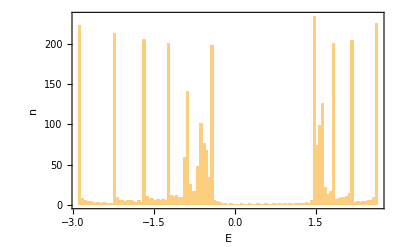

```mathematica
Show[Histogram[val,100],PlotRange-> All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(*zeroMagfield*)
```

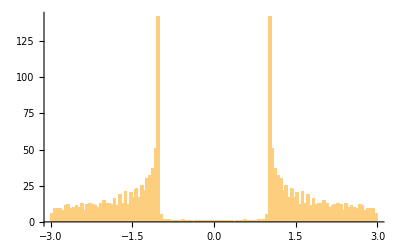

-Graphics-

```mathematica
(** B = 1 **)
```

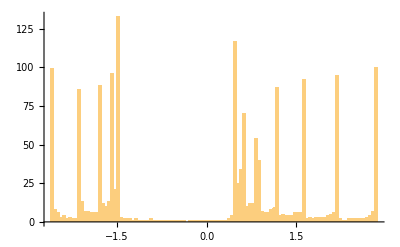

-Graphics-

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val2,vec2,ValVecAHI2,ValAHI2,ValAHIRange2,β];
β=2;
```

```mathematica
{val2,vec2}=Eigensystem[HamiltonianWSM2[1.,3.,(β π)/2,0,0]];
```

```mathematica
ValVecAHI2=SortBy[Transpose[{val2,vec2}],First];
```

```mathematica
ValAHI2=Table[{j,Re[ValVecAHI2[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange2=Table[ValAHI2[[j,2]],{j,1,2 A}];
```

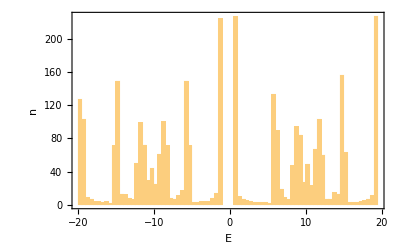

```mathematica
Show[Histogram[val2,100],PlotRange->All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,200]
```

{-3.14159,-3.11018,-3.07876,-3.04734,-3.01593,-2.98451,-2.9531,-2.92168,-2.89027,-2.85885,-2.82743,-2.79602,-2.7646,-2.73319,-2.70177,-2.67035,-2.63894,-2.60752,-2.57611,-2.54469,-2.51327,-2.48186,-2.45044,-2.41903,-2.38761,-2.35619,-2.32478,-2.29336,-2.26195,-2.23053,-2.19911,-2.1677,-2.13628,-2.10487,-2.07345,-2.04204,-2.01062,-1.9792,-1.94779,-1.91637,-1.88496,-1.85354,-1.82212,-1.79071,-1.75929,-1.72788,-1.69646,-1.66504,-1.63363,-1.60221,-1.5708,-1.53938,-1.50796,-1.47655,-1.44513,-1.41372,-1.3823,-1.35088,-1.31947,-1.28805,-1.25664,-1.22522,-1.19381,-1.16239,-1.13097,-1.09956,-1.06814,-1.03673,-1.00531,-0.973894,-0.942478,-0.911062,-0.879646,-0.84823,-0.816814,-0.785398,-0.753982,-0.722566,-0.69115,-0.659734,-0.628319,-0.596903,-0.565487,-0.534071,-0.502655,-0.471239,-0.439823,-0.408407,-0.376991,-0.345575,-0.314159,-0.282743,-0.251327,-0.219911,-0.188496,-0.15708,-0.125664,-0.0942478,-0.0628319,-0.0314159,0.,0.0314159,0.0628319,0.0942478,0.125664,0.15708,0.188496,0.219911,0.251327,0.282743,0.314159,0.345575,0.376991,0.408407,0.439823,0.471239,0.502655,0.534071,0.565487,0.596903,0.628319,0.659734,0.69115,0.722566,0.753982,0.785398,0.816814,0.84823,0.879646,0.911062,0.942478,0.973894,1.00531,1.03673,1.06814,1.09956,1.13097,1.16239,1.19381,1.22522,1.25664,1.28805,1.31947,1.35088,1.3823,1.41372,1.44513,1.47655,1.50796,1.53938,1.5708,1.60221,1.63363,1.66504,1.69646,1.72788,1.75929,1.79071,1.82212,1.85354,1.88496,1.91637,1.94779,1.9792,2.01062,2.04204,2.07345,2.10487,2.13628,2.1677,2.19911,2.23053,2.26195,2.29336,2.32478,2.35619,2.38761,2.41903,2.45044,2.48186,2.51327,2.54469,2.57611,2.60752,2.63894,2.67035,2.70177,2.73319,2.7646,2.79602,2.82743,2.85885,2.89027,2.92168,2.9531,2.98451,3.01593,3.04734,3.07876,3.11018,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

201

```mathematica
(* Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianQAHI[1.0,1.0,1.0,kzVector[[i]]]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] *)
```

```mathematica
(* listplotOfenergyWithKz=Show[ListPlot[b],AxesLabel-> {"kz","Energy"},Frame-> True] *)
```

-Graphics-